Interferometric properties of the state extractable via an operation commuting with the interferometer

In this notebook we will present calculations involving the properties of a (0+2)-photon approximation to squeezed vacuum, and show that it can be extracted using operations commuting with a balanced interferometer.

Matrices  definition

In the Heisenberg picture, one can interpret the action of passive optical elements as modifying the annihilation/creation operators with matrices. The output annihilation/creation operators are described as
, where  is an unitary operator describing the passive element. In the case of two modes, the following unitaries acting on  describe the two basic elements: beamsplitter (matrix B), and balanced phase shift (matrix P). 
We are using the  matrices for easier calculations; this description also allows for easy generalization to squeezing operations. For passive elements, the matrices split into diagonal blocks as , where  acts on the annihilation operators and the conjugate matrix acts on creation operators.

```mathematica
B=({{1, ⅈ, 0, 0}, {ⅈ, 1, 0, 0}, {0, 0, 1, -ⅈ}, {0, 0, -ⅈ, 1}})/(√2); (*beamsplitter*)
P=({{Exp[ⅈ ϕ/2], 0, 0, 0}, {0, Exp[-ⅈ ϕ/2], 0, 0}, {0, 0, Exp[-ⅈ ϕ/2], 0}, {0, 0, 0, Exp[ⅈ ϕ/2]}}); (*balanced phase shift*)
```

We will manipulate expressions involving comp
lex products of annihilation and creation operators with the internal Dot function (used in Wolfram language to denote the standard matrix product), and they are not automatically handled with Mathematica. The following function defines rules simplifying such expressions: removal of numerical factors outside of the dot product, commutation rules, and mode index ordering.

```mathematica
simprules[order_:{2,1}]:={Dot[ops1___,prefactor_ op_,ops2___]/;(MemberQ[{id,Subscript[a, 1],Subscript[A, 1],Subscript[a, 2],Subscript[A, 2]},op]):>prefactor Dot[ops1,op,ops2] (*move non-operator prefactors outside. a.(prefactor b)=prefactor a.b*),
Dot[ops1___,prefactor_ op_,ops2___]/;Head[op]==Dot:>prefactor Dot[ops1,op,ops2]
(*collapse stacked dot products, a.(prefactor b.c).d=prefactor a.b.c.d*),
Dot[ops1_,id,ops2_]:>Dot[ops1,ops2](*collapse identity operators, ×3*),
Dot[id,ops1_,ops2_]:>Dot[ops1,ops2],
Dot[ops1_,ops2_,id]:>Dot[ops1,ops2],

Dot[ops1___,Subscript[a, i_],Subscript[A, j_],ops2___]/;i==j:>Dot[ops1,Subscript[A, j],Subscript[a, i],ops2]+Dot[ops1,id,id,ops2](*move creation operators to the left, adding identity due to commutation rules*),
Dot[ops1___,Subscript[a, i_],Subscript[A, j_],ops2___]/;i!=j:>Dot[ops1,Subscript[A, j],Subscript[a, i],ops2](*move creation ops to the left - they commute for different modes*),
Dot[ops1___,Subscript[a, i_],Subscript[a, j_],ops2___]/;order[[i]]>order[[j]]:>Dot[ops1,Subscript[a, j],Subscript[a, i],ops2],(*enforce mode index ordering for easier calculations, ×2*)
Dot[ops1___,Subscript[A, i_],Subscript[A, j_],ops2___]/;order[[i]]<order[[j]]:>Dot[ops1,Subscript[A, j],Subscript[A, i],ops2],

pref_ Dot[Subscript[a, i_],id]:> pref Dot[id,Subscript[a, i]](*move identity operators to the center, they have to be preserved for easier symbolic calculations*),
pref_ Dot[id,Subscript[A, i_]]:> pref Dot[Subscript[A, i],id]
};
```

If the total expression is presented as sum of terms in the normal ordering (each term having form ), only the terms containing identity operators alone contribute to the vacuum expectation value: , but . The following function defines the rules to simplify the terms (for specific mode indices – later it will be useful to assume that e.g. mode 1 is in vacuum, but mode 2 is in a superposition of finitely many Fock states), leaving only products of identity operators.

```mathematica
expvacuumrules[indices_,order_:{2,1}]:=simprules[order]~Join~{pref_ Dot[ops1__,Subscript[a, i_]]/;MemberQ[indices,i]:>0,
pref_ Dot[Subscript[A, i_],ops1__]/;MemberQ[indices,i]:>0,
pref_ id.id.id:>pref Dot[id,id]};
```

So, the final expression for vacuum expectation value is calculated by the following rule, turning identity operators into ones.

```mathematica
finalizerules={pref_ id.id:>pref 1};
```

Unsqueezed  light

First, let us calculate the phase determination error of an interferometer having coherent state  as one of its inputs, while the second mode is in vacuum. For consistency, we want to use only the vacuum expectation values, and thus the first part is to perform the displacement operation , turning  into .

```mathematica
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}={Subscript[a, 1]+γ id,Subscript[a, 2],Subscript[A, 1]+γ* id,Subscript[A, 2]};
```

Then, the final modes at the interferometer output are modified by the matrices described above. Expectation value of the photon number difference  at the interferometer output will be calculated from the following expression exprC:

```mathematica
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}=Expand/@FullSimplify[B†.P.B.{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}];
exprC=Expand[( Distribute[(Subscript[β, 2]).(Subscript[b, 2])]-Distribute[(Subscript[β, 1]).(Subscript[b, 1])])//.simprules[]]
```

-γ Conjugate[γ] Cos[ϕ/2]^2 id.id-Conjugate[γ] Cos[ϕ/2]^2 id.a_1-γ Cos[ϕ/2]^2 A_1.id-Cos[ϕ/2]^2 A_1.a_1+Cos[ϕ/2]^2 A_2.a_2+2 Conjugate[γ] Cos[ϕ/2] id.a_2 Sin[ϕ/2]+2 Cos[ϕ/2] A_1.a_2 Sin[ϕ/2]+2 γ Cos[ϕ/2] A_2.id Sin[ϕ/2]+2 Cos[ϕ/2] A_2.a_1 Sin[ϕ/2]+γ Conjugate[γ] id.id Sin[ϕ/2]^2+Conjugate[γ] id.a_1 Sin[ϕ/2]^2+γ A_1.id Sin[ϕ/2]^2+A_1.a_1 Sin[ϕ/2]^2-A_2.a_2 Sin[ϕ/2]^2

... while the variance of photon number difference depends on the   (too long to print out):

```mathematica
expr2C=Expand[Distribute[exprC.exprC]//.simprules[]];
```

The  expectation values of the photon number, as well as its second power, and the resulting variance are calculated here to be used later:

```mathematica
firstmomCOH=exprC//.expvacuumrules[{1,2}]/.finalizerules//FullSimplify;

secmomCOH=expr2C//.expvacuumrules[{1,2}]/.finalizerules;
varCOH=secmomCOH-firstmomCOH^2//Expand//FullSimplify//Expand;
Print["⟨N_2-N_1⟩: ",firstmomCOH]
Print["variance of N_2-N_1: ",varCOH]
```

⟨N_2-N_1⟩: -γ Conjugate[γ] Cos[ϕ]

variance of N_2-N_1: Abs[γ]^2

We recover the standard result that the variance is  for the input coherent state .

Squeezed light

If the originally vacuum input mode 2 is squeezed, the operators  are modified by the following matrix:

```mathematica
S=({{1, 0, 0, 0}, {0, Cosh[r], 0, -Sinh[r]}, {0, 0, 1, 0}, {0, -Sinh[r], 0, Cosh[r]}});
```

The first mode is, as before, assumed to be coherent . We can calculate the expectation values using the same procedure:

```mathematica
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}=Expand/@FullSimplify[S.{Subscript[a, 1],Subscript[a, 2],Subscript[A, 1],Subscript[A, 2]}];
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}={Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}+{id γ,0,id γ*,0};
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}=Expand/@FullSimplify[B†.P.B.{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}];
exprS=Expand[( Distribute[(Subscript[β, 2]).(Subscript[b, 2])]-Distribute[(Subscript[β, 1]).(Subscript[b, 1])])//.simprules[]];
expr2S=Expand[Distribute[exprS.exprS]//.simprules[]];

firstmomSQ=exprS//.expvacuumrules[{1,2}]/.finalizerules;
secmomSQ=expr2S//.expvacuumrules[{1,2}]/.finalizerules;
varSQ=secmomSQ-firstmomSQ^2//Expand//FullSimplify//Expand;
Print["⟨N_2-N_1⟩: ",firstmomSQ]
Print["variance of N_2-N_1: ",varSQ]
```

⟨N_2-N_1⟩: -γ Conjugate[γ] Cos[ϕ/2]^2+γ Conjugate[γ] Sin[ϕ/2]^2+Cos[ϕ/2]^2 Sinh[r]^2-Sin[ϕ/2]^2 Sinh[r]^2

variance of N_2-N_1: 1/2 γ Conjugate[γ]+1/2 γ Conjugate[γ] Cosh[2 r]-γ^2 Cosh[r] Sin[ϕ]^2 Sinh[r]-Conjugate[γ]^2 Cosh[r] Sin[ϕ]^2 Sinh[r]+(3 Sinh[r]^2)/4-1/4 Cos[2 ϕ] Sinh[r]^2-γ Conjugate[γ] Cos[2 ϕ] Sinh[r]^2+1/2 Cos[ϕ]^2 Sinh[r] Sinh[3 r]

Quite  complicated, but they are closed form expressions. As we can observe in the following plots of , maximum sensitivity (measured by the derivative with respect to interferometric phase change ) appears around .

```mathematica
Block[{γ=10,r=2},
Plot[{firstmomCOH,firstmomSQ},{ϕ,0,π},PlotLabels->{"coherent |γ="<>ToString[γ]<>"⟩⊗ vacuum","coherent |γ="<>ToString[γ]<>"⟩⊗ squeezed vacuum |r="<>ToString@r<>">"},ImageSize->Large,AxesLabel->{"ϕ","⟨N_2-N_1⟩"}]
]
```

-Graphics-

Error of phase determination around  is calculated using the standard error propagation formula: it is proportional to the square root of variance, and inverse proportional to the derivative of  with respect to . Squeezing improves the phase determination uncertainty significantly:

```mathematica
Block[{γ=10,θ=π/2},
errCOH=(√varCOH)/D[firstmomCOH,ϕ]/.ϕ->θ;
errSQ=(√varSQ)/D[firstmomSQ,ϕ]/.ϕ->θ;
improvement=errSQ/errCOH;
Plot[{errCOH,errSQ},{r,-3,3},PlotRange->{All,{0,1}},AxesLabel->{"squeezing parameter r","phase estimation inaccuracy"},PlotLabels->{"coherent |γ="<>ToString[γ]<>"⟩⊗ vacuum","coherent |γ="<>ToString[γ]<>"⟩⊗ squeezed vacuum |r>"},ImageSize->Large]
]
```

-Graphics-

Zero+One approximation to squeezed light

In  the article, we show that a finite photon number approximation to the squeezed vacuum represented as a superposition of two Fock states () also improves accuracy to some degree, and can be probabilistically prepared by a device commuting with the interferometer given input  . This means that the device can be placed before the interferometer (and used to prepare the input state ), or transform the output state of the interferometer (product of coherent states) into a result of feeding the interferometer with . In short: postprocessing is equivalent to preparation, given certain mathematical criteria. In this section we show that the input state  offers a reduction in phase estimation inaccuracy  (compared to  )  of factor  (asymptotically). First, the calculations are done as previously:

```mathematica
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}=Expand/@FullSimplify[{Subscript[a, 1],Subscript[a, 2],Subscript[A, 1],Subscript[A, 2]},Assumptions->{ϕ>0,r>0}];
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}={Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}+{γ id,0,γ*id,0};
{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]}=Expand/@FullSimplify[B†.P.B.{Subscript[b, 1],Subscript[b, 2],Subscript[β, 1],Subscript[β, 2]},Assumptions->{ϕ>0,r>0}];
%//FullSimplify//MatrixForm;
expr01=Expand[( Distribute[(Subscript[β, 2]).(Subscript[b, 2])]-Distribute[(Subscript[β, 1]).(Subscript[b, 1])])//.simprules[]];
expr201=Expand[Distribute[expr01.expr01]//.simprules[]];
```

Remember that expr01 is a polynomial in the annihilation and creation operators of the input modes (and expr201 is its square):

```mathematica
expr01
```

-γ Conjugate[γ] Cos[ϕ/2]^2 id.id-Conjugate[γ] Cos[ϕ/2]^2 id.a_1-γ Cos[ϕ/2]^2 A_1.id-Cos[ϕ/2]^2 A_1.a_1+Cos[ϕ/2]^2 A_2.a_2+2 Conjugate[γ] Cos[ϕ/2] id.a_2 Sin[ϕ/2]+2 Cos[ϕ/2] A_1.a_2 Sin[ϕ/2]+2 γ Cos[ϕ/2] A_2.id Sin[ϕ/2]+2 Cos[ϕ/2] A_2.a_1 Sin[ϕ/2]+γ Conjugate[γ] id.id Sin[ϕ/2]^2+Conjugate[γ] id.a_1 Sin[ϕ/2]^2+γ A_1.id Sin[ϕ/2]^2+A_1.a_1 Sin[ϕ/2]^2-A_2.a_2 Sin[ϕ/2]^2

We now have to assume that the input mode 1 is in vacuum (which is then displaced by  and fed into the interferometer), and the monomials ending with  (or beginning with  ) do not contribute to the expectation values, while we replace the operators  and  with finite-dimensional matrices (which leads to strict result, since the state has finite maximal photon number), and calculate the expectation values of with the input state .
First, let’s define the state and the matrices:

```mathematica
maxdim=8;
ANN[dim_]:=DiagonalMatrix[Table[√k,{k,dim-1}],1];
vec01=PadRight[{Cos[τ],0,-Sin[τ]},maxdim];
covec01=vec01†//ComplexExpand;
Print["truncated dimension = ",maxdim];
Print["2-photon approximation = ",vec01//MatrixForm];
Print["Truncated annihilation operator = ",ANN[maxdim]//MatrixForm];
```

truncated dimension = 8

2-photon approximation = (Cos[τ]
0
-Sin[τ]
0
0
0
0
0)

Truncated annihilation operator = (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The expectation values are calculated in the following step.

```mathematica
finalizetomatrices[idx_,dim_]:={Subscript[a, idx]->ANN[dim],Subscript[A, idx]->ANN[dim]†,id->IdentityMatrix[dim]}

firstmom01OP=expr01//.expvacuumrules[{1}]/.finalizetomatrices[2,maxdim];
secmom01OP=expr201//.expvacuumrules[{1}]/.finalizetomatrices[2,maxdim];

firstmom01=covec01.firstmom01OP.vec01;
secmom01=covec01.secmom01OP.vec01;
var01=secmom01-firstmom01^2//Expand//FullSimplify//Expand
```

2 γ Conjugate[γ]-γ Conjugate[γ] Cos[2 τ]+(3 Sin[τ]^2)/2-1/2 Cos[2 ϕ] Sin[τ]^2-2 γ Conjugate[γ] Cos[2 ϕ] Sin[τ]^2+Cos[ϕ]^2 Sin[τ] Sin[3 τ]-√2 γ^2 Cos[τ] Sin[τ] Sin[ϕ]^2-√2 Conjugate[γ]^2 Cos[τ] Sin[τ] Sin[ϕ]^2

As before, the maximal accuracy of phase determination is attained around :

```mathematica
Block[{γ=5,τ=π/2},
Plot[{firstmomCOH,firstmom01},{ϕ,0,π},PlotLabels->{"coherent |γ="<>ToString[γ]<>"⟩⊗ vacuum","coherent |γ="<>ToString[γ]<>"⟩⊗ |ψ (τ=π/2)>"},ImageSize->Large,AxesLabel->{"ϕ","⟨N_2-N_1⟩"}]
]
```

-Graphics-

And there is a modest improvement in phase determination inaccuracy around this point:

```mathematica
Block[{γ=100,θ=π/2},
errCOH=(√varCOH)/D[firstmomCOH,ϕ]/.ϕ->θ;
err01=(√var01)/D[firstmom01,ϕ]/.ϕ->θ;
Plot[{errCOH,err01},{τ,0,π/2},PlotRange->{All,{0,2errCOH}},AxesLabel->{"state parameter τ","phase estimation inaccuracy"},PlotLabels->{"coherent |γ="<>ToString[γ]<>"⟩⊗ vacuum","coherent |γ="<>ToString[γ]<>"⟩⊗ |ψ(τ)⟩"},ImageSize->Large]
]
```

-Graphics-

The asymptotic improvement of accuracy can be determined analytically. Let’s assume for simplicity that the input coherent state has real positive displacement γ, and calculate the improvement as a function of  and the parameterization angle :

```mathematica
errCOH=(√varCOH)/D[firstmomCOH,ϕ];
err01=(√(var01//ComplexExpand))/D[firstmom01,ϕ];
improvement=FullSimplify[err01/errCOH/.ϕ->π/2,Assumptions->{γ>0}];
Print["Improvement = ",improvement];
```

Improvement = (γ √(1-(1+2 γ^2) Cos[2 τ]+γ^2 (3-√2 Sin[2 τ])))/(-1+γ^2+Cos[2 τ])

The minimum (and extremum, removed manually) can be determined by postulating that the derivative with respect to  vanishes. The optimal τ can be determined for arbitrary γ, although it is a rather involved function of it. With increasing γ it quickly stabilizes, so let’s determine its asymptotic value instead. For this, let’s calculate the derivative of improvement (squared, for easier calculations) and expand it around , and then find the solutions:

```mathematica
dd=D[improvement^2,τ]//FullSimplify
dd=FullSimplify[Series[dd,{γ,∞,1}]//Normal,Assumptions->{γ>0}];
sols=(Solve[dd==0,τ]//Normal)/.{C[1]->0};
```

1/((-1+γ^2+Cos[2 τ])^3)γ^2 (-3 √2 γ^2-2 √2 γ^2 (-1+γ^2) Cos[2 τ]+√2 γ^2 Cos[4 τ]+2 (1+5 γ^2+2 γ^4) Sin[2 τ]-(1+2 γ^2) Sin[4 τ])

The first solution corresponds to the minimum. It is:

Asymptotically optimal τ = 1/2 ArcTan[1/(√2)]

For this τ, improvement = (√(9-3 √6) γ √(1+3 γ^2))/(-3+√6+3 γ^2)

Asymptotic improvement = √(3-√6)

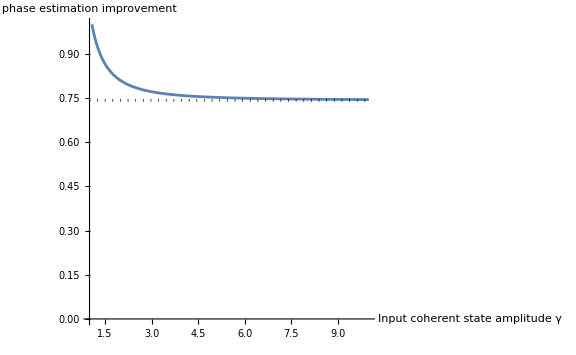

```mathematica
Print["Asymptotically optimal τ = ",τ/.sols[[1]]];
Print["For this τ, improvement = ",improvement/.sols[[1]]//FullSimplify]
Print["Asymptotic improvement = ",Limit[improvement/.sols[[1]],γ->∞]//FullSimplify]
Plot[{improvement/.sols[[1]],√(3-√6)},{γ,1,10},PlotRange->{All,{0,1}},PlotStyle->{Automatic,{Dotted,Black}},AxesLabel->{"Input coherent state amplitude γ","phase estimation improvement"},ImageSize->Large]
```

Characteristic functions

Such a state offers metrological advantage, and here we show that it can be produced from bimodal input of coherent and vacuum states. First, let’s calculate its characteristic function with respect to the  group corresponding to the interferometer action. The  parameter is exactly the angle  of differential phase shift inside the interferometer. 
The  group is a subgroup of the overall  structure, related to arbitrary mode mixing operations. Let us notice that the matrix describing the interferometer action on  operators is indeed a standard 2D rotation, which can be thought of as :

```mathematica
(B†.P.B)[[{1,2},{1,2}]]//FullSimplify//MatrixForm
```

(Cos[ϕ/2] | -Sin[ϕ/2]
Sin[ϕ/2] | Cos[ϕ/2])

Comparing it to the most general form of  matrix , (u | -v*
v | u*), we see that , . With  (and the constraint that ), one can write the matrix as 1/(2z)(1+z^2 | -ⅈ (-1+z^2)
ⅈ (-1+z^2) | 1+z^2), and this can be directly used in the calculation of the characteristic functions related to the interferometer action. 

The initial state is , where   and   is a coherent state, and in the product basis the total state can be written as
 .
Thus, for characteristic function we need only the matrix elements of the  unitary representation between  and   states. They can be found explicitly, and the following code defines the matrix elements (as a  matrix) in the function RedSU2.

```mathematica
statetopoly[j_,ψ_,{z1_,z2_}]:=Sum[(-1)^(j-m)Sqrt[Binomial[2j,j-m]]ψ[[(j-m)+1]]z1^(j+m)z2^(j-m),{m,-j,j}] (* Majorana polynomial for a given state ψ*)
transformpoly[poly_,{z1_,z2_}]:=poly/.Thread[{z1,z2}->({z1,z2}.({{u, -v}, {V, U}}))]

getcoeff[j_,poly_,{z1_,z2_}]:=Module[{coeff},
coeff =Reverse@CoefficientList[poly,{z1,z2},{2j+1,2j+1}];
coeff=Diagonal[coeff];
coeff=coeff * Table[(-1)^(i+1)/Sqrt[Binomial[2*j,i-1]],{i,2j+1}]] (*state for a given polynomial*)

SU2Unitary[j_]:=Module[{basisstates,basispolys,z},
basisstates=IdentityMatrix[2j+1];
basispolys=transformpoly[statetopoly[j,#,{z1,z2}],{z1,z2}]&/@basisstates;
getcoeff[j,#,{z1,z2}]&/@basispolys](*Hilbert state picture of the transformation defined in g: how are basis states transformed?*)
SU2Unitary[jmin_,jmax_]:=DiagonalMatrix[Hold/@Table[SU2Unitary[j],{j,jmin,jmax,1/2}]]//ReleaseHold//ArrayFlatten
SUB1Unitary[j_]:=SU2Unitary[j]/.{u->(z+1/z)/2,v->ⅈ(z-1/z)/2,U->(z+1/z)/2,V->-ⅈ(1/z-z)/2}//Expand
RedSU2[j_]:=({{u^(2j), √Binomial[2j,2] u^(2j-2) V^2}, {√Binomial[2j,2] u^(2j-2) v^2, u^(2j-4) (u^2 U^2-(4j-4) u U v V+(-1+j) (-3+2 j) v^2 V^2)}})
```

Characteristic  function  is parameterized by a complex variable , as mentioned before. The characteristic function can be calculated explicitly by the following code block. Here, for simplification we reparameterize , , perform the summation, and switch back to  variables at the end; the characteristic function  is exactly the overlap between the output of the interferometer and its input state , for .

```mathematica
Block[{j,u=(z+1/z)/2,U=(z+1/z)/2,v=(z-1/z)/(2ⅈ),V=(z-1/z)/(2ⅈ),n},j=n/2;
vec=Exp[-Abs[γ]^2/2]{(γ^n √(1-r))/(√(n!)),-γ^(n-2)/(√((n-2)!))√r};
covec=Exp[-Abs[γ]^2/2]{(Conjugate[γ]^n √(1-r))/(√(n!)),(-Conjugate[γ]^(n-2))/(√((n-2)!))√r};
ex0=covec.RedSU2[j].vec//Expand;
ex1=ex0;
ex2=Simplify[ex1,Assumptions->{n>=2,r>0,r<1}]//Expand;
ex2=ex2/.√(-((-1+n) n (-1+r) r (-2+n)! n!)):>n!√(r(1-r));
ex2=ex2//Simplify;
χ=Sum[ex2,{n,2,∞}]+(ⅇ^(-γ Conjugate[γ]) (1-r) (2 z+(1+z^2) γ Conjugate[γ]))/(2 z);
χ=χ/.{r->1-Cos[τ]^2}//Simplify;
]
```

It  is a rather complex expression involving the defining variables  (coherent state amplitude),  (squeezed state approximation parameter), and  (describing the interferometer phase difference angle). If we plug in the calculated (in the previous section) optimal angle we obtain:

```mathematica
χopt=χ/.{τ->1/2 ArcTan[1/(√2)]}//TrigToExp//Expand//Simplify
```

1/(64 √6 z^4)ⅇ^(-Abs[γ]^2-γ Conjugate[γ]) (8 z^2 (4 (2+√6) ⅇ^(Abs[γ]^2) z^2-4 (2+√6) ⅇ^(γ Conjugate[γ]) z^2+ⅇ^(((1+z)^2 γ Conjugate[γ])/(2 z)) (-2+√6+γ^2+z^2 (4+6 √6-2 γ^2)+z^4 (-2+√6+γ^2)))+8 z (1+z^2) (2 (2+√6) ⅇ^(Abs[γ]^2) z^2-2 (2+√6) ⅇ^(γ Conjugate[γ]) z^2+(-2+√6) ⅇ^(((1+z)^2 γ Conjugate[γ])/(2 z)) (-1+z^2)^2) γ Conjugate[γ]+ⅇ^(((1+z)^2 γ Conjugate[γ])/(2 z)) (-1+z^2)^2 ((-2+√6) γ^2+(-2+√6) z^4 γ^2+z^2 (8-2 (-2+√6) γ^2)) Conjugate[γ]^2)

For , the characteristic function corresponds to the interferometer input being  – coherent in the first port, vacuum in the second. As it turns out, the form of the characteristic function of this state is a (rescaled) generating function of the modified Bessel functions  (see Appendix B of [1], Eq. B.51), and can be decomposed into a sum :

```mathematica
χcoh=χ/.τ->0//FullSimplify//PowerExpand
BesselIGeneratingFn[a_,z_]:=Exp[a(z+1/z)/2]
Print["Is χ_coherentequal to e^(-γ  γ*)(∑^∞)_(k = -∞)z^kI_k(γγ*)? :",χcoh==Exp[-γ γ*]BesselIGeneratingFn[γ γ*,z]//FullSimplify]
Ck=ⅇ^(-γ Conjugate[γ]) BesselI[k,γ Conjugate[γ]];
```

ⅇ^(((-1+z)^2 γ Conjugate[γ])/(2 z))

Is χ_coherentequal to e^(-γ  γ*)(∑^∞)_(k = -∞)z^kI_k(γγ*)? :True

The  characteristic function χopt of the optimal state is the one of the coherent state χcoh multiplied by a expression involving powers of  from  to :

```mathematica
charfnprod=Collect[((χopt/(χcoh z^-4)//FullSimplify)z^-4//Expand),z]
```

3/4+1/(2 √6)-γ^2/(4 √6)+(3 Abs[γ]^4)/32-1/16 √(3/2) Abs[γ]^4+(Abs[γ]^4/64-Abs[γ]^4/(32 √6))/z^4+z^4 (Abs[γ]^4/64-Abs[γ]^4/(32 √6))-Conjugate[γ]^2/(4 √6)+(1/8 γ Conjugate[γ]-(γ Conjugate[γ])/(4 √6))/z^3+z^3 (1/8 γ Conjugate[γ]-(γ Conjugate[γ])/(4 √6))+(-1/8 γ Conjugate[γ]+(γ Conjugate[γ])/(4 √6))/z+z (-1/8 γ Conjugate[γ]+(γ Conjugate[γ])/(4 √6))+(1/8-1/(4 √6)+γ^2/(8 √6)-Abs[γ]^4/16+Abs[γ]^4/(8 √6)+Conjugate[γ]^2/(8 √6))/z^2+z^2 (1/8-1/(4 √6)+γ^2/(8 √6)-Abs[γ]^4/16+Abs[γ]^4/(8 √6)+Conjugate[γ]^2/(8 √6))

Thus, the characteristic function χopt can be written as , where  is convolution of the coherent state coefficients  and the following zero-centered list:

```mathematica
convcoeffs=FullSimplify[CoefficientList[charfnprod z^4 ,z]];
convcoeffs//MatrixForm
```

(-1/192 (-3+√6) Abs[γ]^4
-1/24 (-3+√6) γ Conjugate[γ]
1/48 (6-2 √6+√6 γ^2+(-3+√6) Abs[γ]^4+√6 Conjugate[γ]^2)
1/24 (-3+√6) γ Conjugate[γ]
1/96 (72+8 √6-4 √6 γ^2-3 (-3+√6) Abs[γ]^4-4 √6 Conjugate[γ]^2)
1/24 (-3+√6) γ Conjugate[γ]
1/48 (6-2 √6+√6 γ^2+(-3+√6) Abs[γ]^4+√6 Conjugate[γ]^2)
-1/24 (-3+√6) γ Conjugate[γ]
-1/192 (-3+√6) Abs[γ]^4)

Let' s  assume that the coherent light amplitude is real an positive; then  and the tails of the resulting  determine feasibility of the state extraction. The state can be extracted if , with  and : the extraction succeeds with probability , and with probability  a state corresponding to the probability distribution  is prepared. This is possible if the tails of  (variable Pk) fall off at least as quickly as . Here we calculate the the  coefficients.

```mathematica
convexpr=Sum[FullSimplify[convcoeffs[[i]]/.γ->√a,Assumptions->{a>0}]DiscreteDelta[k+i-5],{i,Length@convcoeffs}];
Cks=FullSimplify[Ck/.γ->√a,Assumptions->{a>0}];
Pk=DiscreteConvolve[Cks,convexpr,k,l]/.l->k;
```

Asymptotically (for ), the Bessel function  has the expansion of (Appendix B of [1], Eq. B.47). Thus, the ratio of tails can be calculated:  with  if . Therefore, a state  can be extracted from  for  with nonzero probability: one has to sacrifice arbitrarily small amplitude of the input coherent state in order to extract the end state.

```mathematica
BesselIasymp[k_,a_]:=( a/2)^k/(k!);
Ckasymp=BesselIasymp[k,a]Exp[-a];
Pkasymp=DiscreteConvolve[Ckasymp,convexpr,k,l]/.{a->(1-ϵ)a,l->k};
Print["Limit of P_k/C_k for k→∞: ",Limit[Pkasymp/Ckasymp//Expand,k->∞,Assumptions->{ϵ<1,ϵ>0}]]
```

Limit of P_k/C_k for k→∞: 0

[1] Francesco Mainardi, Fractional Calculus and Waves in Linear Viscoelasticity, Francesco Mainardi